```mathematica
ClearAll[Manipulation,Polarization,UPolarization,Autoval,Autovec,Eigen,groundstate];
Delta= 0.5;
t=2;
a=1;
L=10000;
Polarization=ConstantArray[0,(L-4)/2+1];
UPolarization=ConstantArray[0,(L-4)/2+1];
Manipulation= Table[0,{j,1,9},{k,1,(L-4)/2+1}];
```

```mathematica
ClearAll[Polarization,UPolarization,Autoval,Autovec,Eigen,groundstate];Polarization=ConstantArray[0,(L-4)/2+1];
UPolarization=ConstantArray[0,(L-4)/2+1];
For[n=4,n≤L-2,n+=2,{
H=ConstantArray[0,{n,n}],
For[i=1,i≤ n-1, i++,{H[[i,i]]= Delta *(-1)^i, H[[i,i+1]]=-t, H[[i+1,i]]=-t}],
H[[n,n]]=Delta * (-1)^n,
Eigen=Eigensystem[H],
{Autoval,Autovec}=Eigen,
groundstate= Sum[Autovec[[j]],{j,1,n}],
groundstate=groundstate/Sqrt[n],
X=ConstantArray[0,{n,n}],
For[i=1,i≤ n, i+=2,{X[[i,i]]= a*(1/4 +(i-1)), X[[i+1,i+1]]=a*(3/4+(i-1))}],
d = (groundstate.(Autovec X Transpose[Autovec]-1)).groundstate,
UPolarization[[(n-4)/2+1]]= d
}];
```

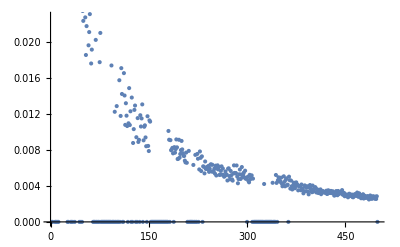

```mathematica
ListPlot[UPolarization]
```

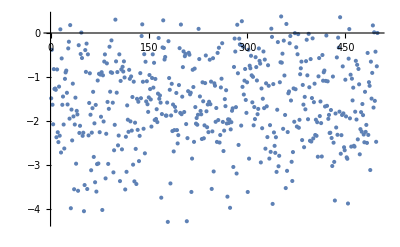

```mathematica
ListPlot[UPolarization]
```

```mathematica
Export["ManipulationProgressiveDovert10.dat",Manipulation]
```

ManipulationProgressiveDovert10.dat

```mathematica
ClearAll[Polarization,UPolarization,Autoval,Autovec,Eigen,groundstate,d,X,H];Polarization=ConstantArray[0,(L-4)/2+1];
UPolarization=ConstantArray[0,(L-4)/2+1];
For[n=4,n≤L-2,n+=2,{
H=ConstantArray[0,{n,n}],
For[i=1,i≤ n-1, i++,{H[[i,i]]= Delta *(-1)^i, H[[i,i+1]]=-t, H[[i+1,i]]=-t}],
H[[n,n]]=Delta * (-1)^n,
Eigen=Eigensystem[H],
{Autoval,Autovec}=Eigen,
For[j=1,j≤n,j+=1,{groundstate=ConstantArray[0,n],
If[Autoval[[j]]≤0, groundstate=groundstate+2*a*Autovec[[j]],groundstate=groundstate]}],
groundstate=groundstate/Sqrt[n],
X=ConstantArray[0,{n,n}],
For[i=1,i≤ n, i+=2,{X[[i,i]]= a*(1/4 +(i-1)), X[[i+1,i+1]]=a*(3/4+(i-1))}],
d = (groundstate.(Transpose[Autovec] X Autovec-Autovec)).groundstate,
UPolarization[[(n-4)/2+1]]= d
}];
```

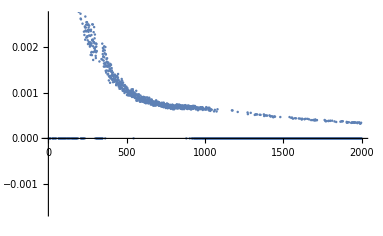

```mathematica
ListPlot[UPolarization]
```

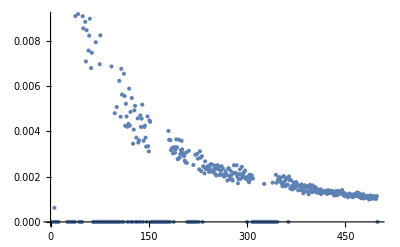

```mathematica
ListPlot[UPolarization]
```

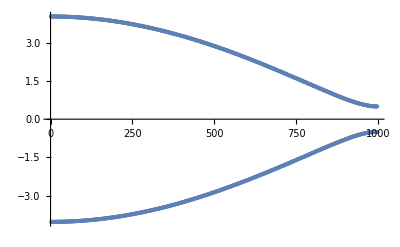

```mathematica
ListPlot[Autoval]
```